Figure (linearPolarizationFig1.eps) showing the electric and magnetic field directions for a linearly polarized field propagating at a fixed angle to the horizontal in the transverse plane.

```mathematica
<<peeters` ;
peeters`setGitDir[ "../project/figures/GAelectrodynamics" ]
```

/Users/pjoot/project/figures/GAelectrodynamics

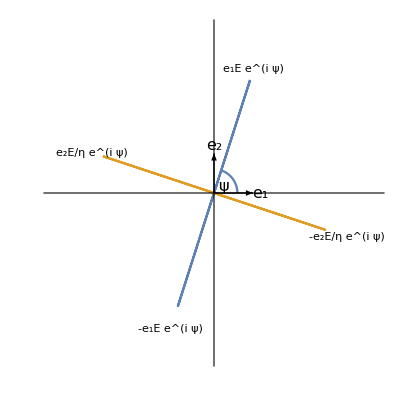

```mathematica
ClearAll[p1, bold, pt, fs]
pt[r_, t_] := r{Cos[t],Sin[t]};
bold = Style[ #, Bold] &;
fs:= Style[ #, FontSize -> 16 ]&;

p1 = Module[{e1,e2, psi, r,o, vecE, te1, te2, vecH, rho},
{e1,e2} = IdentityMatrix[2];
psi = .4 Pi;
rho = 3;
r = rho{-1.4,1.4};
o = {0,0};
vecE = pt[rho,psi] ;
vecH = pt[rho,psi + Pi/2];
te1 = Subscript["e"// bold, 1]//fs;
te2 = Subscript["e"// bold, 2]//fs;
Show[{
ParametricPlot[{vecE Cos[ t ],vecH Cos[ t ]}, {t, 0, 2 Pi}, 
PlotRange -> {r,r},
Ticks -> None
],
ParametricPlot[(rho/5){Cos[t],Sin[t]},{t,0,psi}],
Graphics[{
Arrow[{o, e1}],
Arrow[{o, e2}],
Text[te1, 1.2 e1],
Text[te2, 1.2 e2],
Text[Row[{te1, "E e^(i ψ)"//fs}], 1.1 vecE],
Text[Row[{"-"//fs, te1, "E e^(i ψ)"//fs}], -1.2 vecE],
Text[Row[{te2, "E/η e^(i ψ)"//fs}], 1.1 vecH],
Text[Row[{"-"//fs, te2, "E/η e^(i ψ)"//fs}], -1.2 vecH],
Text[ "ψ"//fs, pt[0.3,psi/2]]
},
AspectRatio-> 1 ]
}]
]
```

```mathematica
peeters`exportForLatex["linearPolarizationFig1", p1]
```

{linearPolarizationFig1.eps,linearPolarizationFig1pn.png}